## MLR Potentials

This code will reproduce the potential curves for the X^1 Σ_g^+ and a^3 Σ_u^+states of ^7 Li_2 using the MLR model outlined in Le Roy et al. Chem. Phys. 131, 204309 (2009), Le Roy et al. Mol. Phys. 109, 3 (2011). and Le Roy and Dattani, Mol. Spec. 268 (2011). Parameters have units of energy in cm^-1and units of length in Å. The final potentials have units of energy in Hartree and units of length in a_0.

```mathematica
sde = 8516.7084;
tde = 333.758;
sre = 2.6729932;
tre = 4.17005000;
sref = 3.85;
tref = 8.0;
sc6 = 6.71527 * 10^6;
sc8 = 1.12588 * 10^8;
sc10 = 2.78604 * 10^9;
tc6 = 6.7185*10^6;
tc8 =1.12629*10^8;
tc10 = 2.78683*10^9;
p = 5;
q = 3;
ρ1 = 0.54;
sβcf1 = {-2.89828701, -1.309265,-2.018507, -1.38162,-1.21933, 0.3463, 0.1061,-0.1886,1.671,10.943,3.944,-27.23,-11.49,56.7, 38.9,-37.4, -33.0};
tβcf =  {-0.51608,-0.09782, 0.1137, -0.0248};
```

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
AngstrominBohr = 1/0.529177210903;
```

```mathematica
DDS[r_,m_,bds_,cds_,ρ_,s_]:= (1-Exp[-(ρ r)(bds/m+(cds (ρ r))/m^(1/2))])^(m+s);
DDSTriplet[m_,r_]:= DDS[r,m,3.30,0.423,0.54,-1];
```

```mathematica
ulr[r_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= dcf6 c6/r^6+dcf8 c8/r^8+dcf10 c10/r^10;
y[rp_,r_,p_]:=(r^p-rp^p)/(r^p+rp^p);
βinf[de_,re_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= Log[(2 de)/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]];
βinfT=βinf[tde,tre,DDSTriplet[6,tre],DDSTriplet[8,tre],DDSTriplet[10,tre],tc6,tc8,tc10];
βinfS=βinf[sde,sre,1,1,1,sc6,sc8,sc10];
β[r_,βcf_,βinf_,ypeq_,ypref_,yqref_]:= βinf ypref+(1-ypref)* Sum[βcf[[j+1]]*(yqref)^j,{j,0,Length[βcf]-1}];
```

```mathematica
βTriplet[r_]:= βinfT*y[tref,r,5]+(1-y[tref,r,5])*Sum[tβcf[[j+1]]*y[tref,r,3]^j,{j,0,Length[tβcf]-1}];
ulrTriplet[r_]:= DDSTriplet[6,r] tc6/r^6+DDSTriplet[8,r] tc8/r^8+DDSTriplet[10,r] tc10/r^10;
TripletMLR[r_]:= tde(1-ulrTriplet[r]/ulrTriplet[tre]*Exp[-βTriplet[r]*y[tre,r,p]])^2-tde;
VMLR[r_,re_,de_,β_,ypeq_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= de(1-ulr[r,dcf6,dcf8,dcf10,c6,c8,c10]/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]*Exp[-β ypeq])^2-de;
SingletMLR[r_]:= VMLR[r,sre,sde,β[r,sβcf1,βinf[sde,sre,1,1,1,sc6,sc8,sc10],y[sre,r,p],y[sref,r,p],y[sref,r,q]],y[sre,r,p],1,1,1,sc6,sc8,sc10]
```

```mathematica
Rmax=200;
Rmin=0.005;
NR =10000;
dR=(Rmax-Rmin)/NR;
RGrid =Table[Rmin+dR i,{i,1,NR}];
TripletMLRdat = Table[{RGrid[[i]],TripletMLR[RGrid[[i]]]},{i,1,NR}];
TripletMLRHBdat =Table[{RGrid[[i]]*AngstrominBohr,TripletMLRdat[[i,2]]*invcminHartree},{i,1,NR}];
TripletHBMLR=Interpolation[TripletMLRHBdat]
```

General::munfl: Exp[-708.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.719] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.958] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction[…]

```mathematica
SingletMLRdat = Table[{RGrid[[i]],SingletMLR[RGrid[[i]]]},{i,1,NR}];
SingletMLRHBdat =Table[{RGrid[[i]]*AngstrominBohr,SingletMLRdat[[i,2]]*invcminHartree},{i,1,NR}];
SingletHBMLR=Interpolation[SingletMLRHBdat]
```

InterpolatingFunction[…]

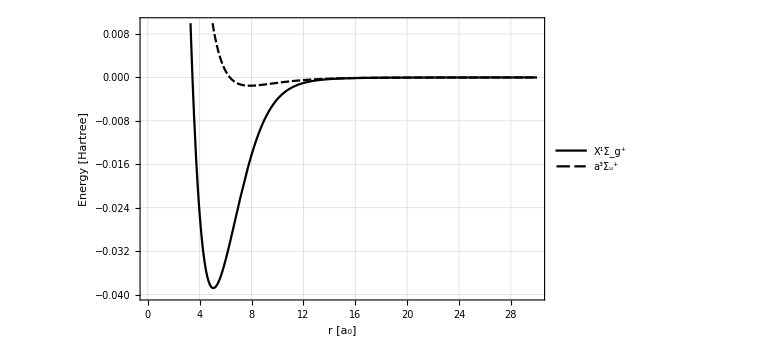

```mathematica
Plot[{SingletHBMLR[r],TripletHBMLR[r]},{r,2.0,30},PlotRange->{-0.040,0.010},ImageSize->Large,GridLines->Automatic,Frame->True,FrameLabel->{"r [a_0]","Energy [Hartree]"},LabelStyle->Medium,PlotLegends->{"X^1Σ_g^+","a^3Σ_u^+"}]
```

## ^7 Li +^7 Li Collision

In this section, we define the full potential governing the interaction between two ^7 Li atoms. The full Hamiltonian for a Li_2collision is

H = -ℏ^2/(2 μ) d^2/(d r^2) + P_0 V_0(r) + P_1 V_1(r) +(l(l+1)ℏ^2)/(2 μ r^2)+ ∑A_i(s_i· i_i) + (g_s^(i) μ_B s_z^(i)+ g_i^(i)μ_N i_z^(i))B

here P_0 and P_1 are the singlet and triplet projection operators, V_0(r) is the potential for the X^1(Σ^+)_g state, V_1(r) is the potential for the a^3(Σ^+)_u state, μ_B is the Bohr magneton, μ_N is the nuclear magneton, B is the magnitude of an external magnetic field, applied along the z-axis, g_s is the electronic gyromagnetic ratio, g_i is the nuclear gyromagnetic ratio, A is the hyperfine constant, s is the electronic spin, i is the nuclear spin, s_z is the component of electronic spin along the z-axis, i_z is the component of the nuclear spin along the z-axis, and the sum is over the two atoms.

```mathematica
Li7s = 1/2;
Li7i = 3/2;
Li7gs = 2.0;
mF2basis = {{1,1,1,1},{1,1,2,1},{1,0,2,2},{2,0,2,2},{2,1,2,1}};
Li7gi = 2.170903;
Li7ATHz = 401.75204335 * 10^-6;
Li7Ainvcm = (Li7ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
Li7AH = Li7Ainvcm*invcminHartree;
μb = (9.27400994*10^-24)/(6.626*10^-34)*10^-12*(1/10^4);
μn = (5.0507837461*10^-27)/(6.626*10^-34)*10^-12*(1/10^4);
μbinvcm = (μb *6.626*10^-34*10^12)/(1.986*10^-23);
μninvcm = (μn *6.626*10^-34*10^12)/(1.986*10^-23);
μbH=μbinvcm*invcminHartree;
μnH=μninvcm*invcminHartree;
```

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μbH B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μnH B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

```mathematica
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,4]]]+HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
HZsymLi7[B_]=FullSimplify[HZsym[0,0,B]];
SProjSymLi7 = {{3/16,(√(3/2))/8,-(√3)/8,(√3)/8,-3/16},{(√(3/2))/8,1/8,-1/(4 √2),1/(4 √2),-(√(3/2))/8},{-(√3)/8,-1/(4 √2),1/4,-1/4,(√3)/8},{(√3)/8,1/(4 √2),-1/4,1/4,-(√3)/8},{-3/16,-(√(3/2))/8,(√3)/8,-(√3)/8,3/16}};
TProjSymLi7 = {{13/16,-(√(3/2))/8,(√3)/8,-(√3)/8,3/16},{-(√(3/2))/8,7/8,1/(4 √2),-1/(4 √2),(√(3/2))/8},{(√3)/8,1/(4 √2),3/4,1/4,-(√3)/8},{-(√3)/8,-1/(4 √2),1/4,3/4,(√3)/8},{3/16,(√(3/2))/8,-(√3)/8,(√3)/8,13/16}};
```

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-3/2},{1,-1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-1/2},{1,-1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
MatrixForm[TProjSymLi7]
```

(13/16 | -(√(3/2))/8 | (√3)/8 | -(√3)/8 | 3/16
-(√(3/2))/8 | 7/8 | 1/(4 √2) | -1/(4 √2) | (√(3/2))/8
(√3)/8 | 1/(4 √2) | 3/4 | 1/4 | -(√3)/8
-(√3)/8 | -1/(4 √2) | 1/4 | 3/4 | (√3)/8
3/16 | (√(3/2))/8 | -(√3)/8 | (√3)/8 | 13/16)

```mathematica
Htotal[r_,B_]= HZsymLi7[B]+TProjSymLi7*TripletHBMLR[r]+SProjSymLi7*SingletHBMLR[r];
```

### Single Channel QDT Calculation to Determine the Scattering Lengths and Quantum Defects of the Singlet and Triplet Potentials

We first define the (irregular) zero-energy solution χ_-(r)  for an -C_6/r^6 potential (which will be used for constructing the Milne solutions) and the Riccati functions (which will be used later to calculate the positive-energy MQDT parameters η, 𝒜, and 𝒢).

```mathematica
χminus[r_,l_]:= Sqrt[r] BesselJ[1/4(2l+1),1/(2 r^2) ];
χmprime[r_,l_]:= D[χminus[rp,l],rp]/.rp->r;
f[l_,k_,r_]:=Sqrt[k/π] r SphericalBesselJ[l,k r];
g[l_,k_,r_]:= Sqrt[k/π] r SphericalBesselY[l,k r];
dfdr[l_,k_,r_]:=D[f[l,k,rp],rp]/.rp->r; 
dgdr[l_,k_,r_]:=D[g[l,k,rp],rp]/. rp->r;
```

Module for constructing reference wave-functions g^0(r) and f^0(r)

```mathematica
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=α';
g0=- α[r]Cos[ϕ+phaseint[r]];
f0= α[r]Sin[ϕ+phaseint[r]];
f0p=αp[r]/α[r] f0-1/α[r]^2 g0;
g0p=αp[r]/α[r] g0+1/α[r]^2 f0;
χm=χminus[r,l];
χmp=χmprime[r,l];
{f0,g0,f0p,g0p,χm,χmp}]
```

Module for calculating alpha and phase integral functions using the Milne phase-amplitude method.

```mathematica
CalcAlphaPhaseIntFun2[Ε_,l_,rx_,rf_,r_,nr_,μ_,C6_,C8_,C10_]:= Module[{k,bC1,bC2, rGrid,PhaseIntTable,rp,PhaseIntFun,αfun,α},
k=Sqrt[2 μ (Ε+C6/r^6+C8/r^8+C10/r^8-(l(l+1))/(2 μ r^2))];
bC1 = 1/Sqrt[2μ(Ε + C6/r^6+C8/r^8+C10/r^8-(l(l+1))/r^2)^(1/2)]/.r->rx;
bC2 = D[1/Sqrt[2μ(Ε + C6/r^6+C8/r^8+C10/r^8-(l(l+1))/r^2)^(1/2)],r]/.r->rx;
αfun = NDSolveValue[{α''[r]+ k^2 α[r]-1/α[r]^3== 0,α[rx]== bC1,α'[rx]== bC2},α,{r,rx,rf}];
rGrid = Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable = Flatten[{0,Table[NIntegrate[1/αfun[rp]^2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}];
PhaseIntFun = Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[1;;i]]]},{i,1,nr}]];
Return[{αfun,PhaseIntFun}]
]
```

Module for calculating the log-derivative of the interior solution at the matching radius r_m.

```mathematica
CalcY[Ε_,l_,rmin_,rmax_,μ_,r0_,U_,r_]:=Module[{Y,u,ψin,ψinp,rp},
ψin=NDSolveValue[{-1/(2 μ)u''[r]+ (U[r]+(l(l+1))/(2 μ r^2))*u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
ψinp=ψin';
Y = ψinp[r]/ψin[r]/.r->r0;
Return[Y]
]
```

Modules for calculate the short-range reaction matrix K^sr, physical K-matrix, and plotting the wavefunction

```mathematica
CalCKsr[Ε_,r0_,l_,rx_,rf_,nr_,r_,ϕ_,rmin_,rmax_,μ_,U_,C6_,C8_,C10_]:= Module[{Y,kin,f0,g0,f0p,g0p,χm,χmp,Ksr,αfun,PhaseIntfun},
Y=CalcY[Ε,l,rmin,rmax,μ,r0,U,r];
{αfun,PhaseIntfun} = CalcAlphaPhaseIntFun2[Ε,l,rx,rf,r,nr,μ,C6,C8,C10];
{f0,g0,f0p,g0p,χm,χmp} = basepairs[l,ϕ,αfun,PhaseIntfun,r0];
Ksr = (Y f0 -f0p)/(Y g0 -g0p);
Return[Ksr]
]
CalcK[Ε_,r0_,l_,rx_,rf_,nr_,r_,ϕ_,rmin_,rmax_,μ_,U_,C6_,C8_,C10_]:= Module[{f0,g0,f0p,g0p,χm,χmp,Ksr,αfun,PhaseIntfun,K,k,F,dF,G,dG},
{αfun,PhaseIntfun} = CalcAlphaPhaseIntFun2[Ε,l,rx,rf,r,nr,μ,C6,C8,C10];
{f0,g0,f0p,g0p,χm,χmp} = basepairs[l,ϕ,αfun,PhaseIntfun,r];
Ksr = CalCKsr[Ε,r0,l,rx,rf,nr,r,ϕ,rmin,rmax,μ,U,C6,C8,C10];
k = Sqrt[2 μ Ε];
F = f[l,k,r];
dF = dfdr[l,k,r];
G = g[l,k,r];
dG = dgdr[l,k,r];
K = ((f0 dF - f0p F) - Ksr (g0 dF - g0p F))/((f0 dG - f0p G) - Ksr (g0 dG - g0p G))/.r->rf;
K
]
```

```mathematica
PlotWavefunction[Ε_,r0_,l_,rx_,rf_,nr_,r_,ϕ_,μ_,U_,rmax_,rmin_,C6_,C8_,C10_]:= Module[{rp,u,f0,g0,f0p,g0p,χm,χmp,Ksr,αfun,PhaseIntfun,K,C, ψlr,ψin,ψinp,s},
{αfun,PhaseIntfun} = CalcAlphaPhaseIntFun2[Ε,l,rx,rf,r,nr,μ,C6,C8,C10];
{f0,g0,f0p,g0p,χm,χmp} = basepairs[l,ϕ,αfun,PhaseIntfun,r];
Ksr = CalCKsr[Ε,r0,l,rx,rf,nr,r,ϕ,rmin,rmax,μ,U,C6,C8,C10];
ψin = NDSolveValue[{-1/(2 μ)u''[r]+ (U[r]+(l(l+1))/(2 μ r^2))*u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
ψinp[s_] = D[ψin[rp],rp]/.rp->s;
C= (g0 ψinp[r]- g0p ψin[r])/(g0 f0p - f0 g0p)/.r->r0;
Plot[Piecewise[{{ψin[r],r<r0},{C f0-C Ksr g0,r0<r<rf}}],{r,rx,r0},ImageSize->Large]
]
```

```mathematica
TripletLi7[r_,a_]:= TripletHBMLR[r]+If[r<tre*AngstrominBohr, a(r-tre*AngstrominBohr)^2,0];
SingletLi7[r_,a_]:=SingletHBMLR[r]+If[r<sre*AngstrominBohr, a(r-sre*AngstrominBohr)^2,0];
```

```mathematica
μLi7 = 6394.7;
```

```mathematica
CalcCotanDeltaTriplet[Εtest_,rmax_,rmin_,μ_,a_]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2,u},
r1=0.95 rmax;
r2=0.99rmax;
k=√(2 μ Εtest);
sol=NDSolve[{-1/(2 μ)u''[r]+TripletLi7[r,a] u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]

CalcERETriplet[rmax_,rmin_,ΕMin_,ΕMax_,μ_,a_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{2μ Εtest,√(2μ Εtest)CalcCotanDeltaTriplet[Εtest,rmax,rmin,μ,a]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
CalcERETriplet[370,2,10^-12,10^-11,μLi7,2.805*10^-7]
```

NDSolve::underdet: There are more dependent variables, {TripletHBMLR[r],u$47649[r]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {(If[r<Times[«2»],2.805×10^-7 Power[«2»],0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::underdet: There are more dependent variables, {TripletHBMLR[r],u$47680[r]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {(If[r<Times[«2»],2.805×10^-7 Power[«2»],0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::underdet: There are more dependent variables, {TripletHBMLR[r],u$47698[r]}, than equations, so the system is underdetermined.

General::stop: Further output of NDSolve::underdet will be suppressed during this calculation.

{-(3.31662/((0.000138286 (0.999142 (u$47649[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000})-0.99921 (u$47649[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000})))/(-0.0414131 (u$47649[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000})+0.0397407 (u$47649[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000}))+(0.000161892 (0.99837 (u$47680[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000})-0.998499 (u$47680[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000})))/(-0.0570693 (u$47680[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000})+0.0547659 (u$47680[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000}))+(0.000161661 (0.997599 (u$47698[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000})-0.997789 (u$47698[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000})))/(-0.0692617 (u$47698[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000})+0.0664675 (u$47698[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000}))+(0.000145753 (0.996827 (u$47710[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000})-0.997078 (u$47710[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000})))/(-0.0795982 (u$47710[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000})+0.0763885 (u$47710[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000}))+(0.000117824 (0.996056 (u$47718[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000})-0.996368 (u$47718[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000})))/(-0.0887298 (u$47718[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000})+0.0851536 (u$47718[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000}))+(0.0000799669 (0.995285 (u$47726[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000})-0.995658 (u$47726[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000})))/(-0.0969974 (u$47726[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000})+0.0930899 (u$47726[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000}))+(0.0000335463 (0.994514 (u$47734[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000})-0.994948 (u$47734[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000})))/(-0.104606 (u$47734[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000})+0.100394 (u$47734[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000}))-(0.0000204728 (0.993743 (u$47742[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000})-0.994238 (u$47742[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000})))/(-0.111691 (u$47742[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000})+0.107196 (u$47742[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000}))-(0.0000813681 (0.992973 (u$47750[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000})-0.993528 (u$47750[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000})))/(-0.118345 (u$47750[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000})+0.113584 (u$47750[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000}))-(0.000148577 (0.992202 (u$47758[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000})-0.992819 (u$47758[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000})))/(-0.124638 (u$47758[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000})+0.119627 (u$47758[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000}))-(0.000221645 (0.991432 (u$47766[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000})-0.99211 (u$47766[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000})))/(-0.130623 (u$47766[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000})+0.125374 (u$47766[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000})))),7.61379×10^6 (-((0.000117311 (0.999142 (u$47649[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000})-0.99921 (u$47649[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000})))/(-0.0414131 (u$47649[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000})+0.0397407 (u$47649[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000})))-(0.000129362 (0.99837 (u$47680[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000})-0.998499 (u$47680[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000})))/(-0.0570693 (u$47680[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000})+0.0547659 (u$47680[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000}))-(0.000117779 (0.997599 (u$47698[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000})-0.997789 (u$47698[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000})))/(-0.0692617 (u$47698[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000})+0.0664675 (u$47698[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000}))-(0.0000902609 (0.996827 (u$47710[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000})-0.997078 (u$47710[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000})))/(-0.0795982 (u$47710[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000})+0.0763885 (u$47710[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000}))-(0.0000503208 (0.996056 (u$47718[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000})-0.996368 (u$47718[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000})))/(-0.0887298 (u$47718[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000})+0.0851536 (u$47718[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000}))+(1.01432×10^-19 (0.995285 (u$47726[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000})-0.995658 (u$47726[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000})))/(-0.0969974 (u$47726[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000})+0.0930899 (u$47726[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000}))+(0.0000593552 (0.994514 (u$47734[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000})-0.994948 (u$47734[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000})))/(-0.104606 (u$47734[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000})+0.100394 (u$47734[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000}))+(0.000126783 (0.993743 (u$47742[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000})-0.994238 (u$47742[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000})))/(-0.111691 (u$47742[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000})+0.107196 (u$47742[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000}))+(0.000201557 (0.992973 (u$47750[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000})-0.993528 (u$47750[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000})))/(-0.118345 (u$47750[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000})+0.113584 (u$47750[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000}))+(0.000283106 (0.992202 (u$47758[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000})-0.992819 (u$47758[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000})))/(-0.124638 (u$47758[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000})+0.119627 (u$47758[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000}))+(0.00037097 (0.991432 (u$47766[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000})-0.99211 (u$47766[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000})))/(-0.130623 (u$47766[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000})+0.125374 (u$47766[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000}))),{{1.27894×10^-8,(0.00011309 (0.999142 (u$47649[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000})-0.99921 (u$47649[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000})))/(-0.0414131 (u$47649[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000})+0.0397407 (u$47649[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47649[r]-0.0000781898 u$47649''[r]==u$47649[r]/1000000000000,u$47649[2]==0,u$47649'[2]==1/10000000000}))},{2.42999×10^-8,(0.000155884 (0.99837 (u$47680[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000})-0.998499 (u$47680[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000})))/(-0.0570693 (u$47680[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000})+0.0547659 (u$47680[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47680[r]-0.0000781898 u$47680''[r]==(19 u$47680[r])/10000000000000,u$47680[2]==0,u$47680'[2]==1/10000000000}))},{3.58103×10^-8,(0.000189236 (0.997599 (u$47698[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000})-0.997789 (u$47698[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000})))/(-0.0692617 (u$47698[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000})+0.0664675 (u$47698[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47698[r]-0.0000781898 u$47698''[r]==(7 u$47698[r])/2500000000000,u$47698[2]==0,u$47698'[2]==1/10000000000}))},{4.73208×10^-8,(0.000217533 (0.996827 (u$47710[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000})-0.997078 (u$47710[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000})))/(-0.0795982 (u$47710[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000})+0.0763885 (u$47710[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47710[r]-0.0000781898 u$47710''[r]==(37 u$47710[r])/10000000000000,u$47710[2]==0,u$47710'[2]==1/10000000000}))},{5.88312×10^-8,(0.000242552 (0.996056 (u$47718[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000})-0.996368 (u$47718[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000})))/(-0.0887298 (u$47718[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000})+0.0851536 (u$47718[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47718[r]-0.0000781898 u$47718''[r]==(23 u$47718[r])/5000000000000,u$47718[2]==0,u$47718'[2]==1/10000000000}))},{7.03417×10^-8,(0.00026522 (0.995285 (u$47726[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000})-0.995658 (u$47726[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000})))/(-0.0969974 (u$47726[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000})+0.0930899 (u$47726[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47726[r]-0.0000781898 u$47726''[r]==(11 u$47726[r])/2000000000000,u$47726[2]==0,u$47726'[2]==1/10000000000}))},{8.18522×10^-8,(0.000286098 (0.994514 (u$47734[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000})-0.994948 (u$47734[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000})))/(-0.104606 (u$47734[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000})+0.100394 (u$47734[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47734[r]-0.0000781898 u$47734''[r]==u$47734[r]/156250000000,u$47734[2]==0,u$47734'[2]==1/10000000000}))},{9.33626×10^-8,(0.000305553 (0.993743 (u$47742[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000})-0.994238 (u$47742[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000})))/(-0.111691 (u$47742[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000})+0.107196 (u$47742[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47742[r]-0.0000781898 u$47742''[r]==(73 u$47742[r])/10000000000000,u$47742[2]==0,u$47742'[2]==1/10000000000}))},{1.04873×10^-7,(0.000323841 (0.992973 (u$47750[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000})-0.993528 (u$47750[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000})))/(-0.118345 (u$47750[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000})+0.113584 (u$47750[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47750[r]-0.0000781898 u$47750''[r]==(41 u$47750[r])/5000000000000,u$47750[2]==0,u$47750'[2]==1/10000000000}))},{1.16384×10^-7,(0.00034115 (0.992202 (u$47758[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000})-0.992819 (u$47758[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000})))/(-0.124638 (u$47758[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000})+0.119627 (u$47758[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47758[r]-0.0000781898 u$47758''[r]==(91 u$47758[r])/10000000000000,u$47758[2]==0,u$47758'[2]==1/10000000000}))},{1.27894×10^-7,(0.000357623 (0.991432 (u$47766[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000})-0.99211 (u$47766[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000})))/(-0.130623 (u$47766[351.5]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000})+0.125374 (u$47766[366.3]/.{(If[r<1.88973 tre,2.805×10^-7 (r-tre AngstrominBohr)^2,0]+TripletHBMLR[r]) u$47766[r]-0.0000781898 u$47766''[r]==u$47766[r]/100000000000,u$47766[2]==0,u$47766'[2]==1/10000000000}))}}}

```mathematica
atp = 2.805*10^-7;
```

```mathematica
TripletHBMLRNew[r_]:= TripletLi7[r,atp];
```

```mathematica
CalcCotanDeltaSinglet[Εtest_,rmax_,rmin_,μ_,a_]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2,u},
r1=0.95 rmax;
r2=0.99rmax;
k=√(2 μ Εtest);
sol=NDSolve[{-1/(2 μ)u''[r]+SingletLi7[r,a] u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]

CalcERESinglet[rmax_,rmin_,ΕMin_,ΕMax_,μ_,a_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{2μ Εtest,√(2μ Εtest)CalcCotanDeltaSinglet[Εtest,rmax,rmin,μ,a]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
CalcERESinglet[370,2,10^-12,10^-11,μLi7,0]
```

{34.3313,52.0365,{{1.27894×10^-8,-0.0291276},{2.42999×10^-8,-0.0291273},{3.58103×10^-8,-0.029127},{4.73208×10^-8,-0.0291267},{5.88312×10^-8,-0.0291264},{7.03417×10^-8,-0.0291261},{8.18522×10^-8,-0.0291258},{9.33626×10^-8,-0.0291255},{1.04873×10^-7,-0.0291252},{1.16384×10^-7,-0.0291249},{1.27894×10^-7,-0.0291246}}}

## Multichannel Scattering Calculation

### Frame Transformation Method for Calculating K^sr

References:

J. P. Burke. “Theoretical Investigation of Cold Alkali Atom Collisions.” University of Colorado, PhD Thesis (1999)

From Section 4.3: Frame Transformation Approximation

The short range reaction matrix is approximated by the frame transformation (FT) expression

(K^sr)_(i,i')=∑_λ ⟨i|λ⟩tan(πμ_λ(OverBar[ϵ_λ]))⟨λ|i'⟩

where ⟨i|λ⟩ represents the unitary transformation that connects the short range singlet-triplet, or molecular, basis λ=(s_a s_b)S(i_a i_b)I F M with the asymptotic hyperfine basis i=(s_a i_a)f_a(s_b i_b)f_b F M and OverBar[ϵ_λ]=∑_i ϵ_i|⟨i|λ⟩|^2. Moreover, ⟨i|λ⟩ is understood to the transformation between symmetrized kets if the particles are identical.

##### Energy-Independent FT Approximation

In this approximation, only the zero energy values of the quantum defects are used and Equation 41 simplifies to

(K^sr)_(i,i')=∑_λ ⟨i|λ⟩tan(πμ_λ(0))⟨λ|i'⟩.

K = (A^(1/2)((K̃)^-1+G))^-1 A^(1/2)

S =e^iη (1+i K)/(1-i K)e^iη.

Burke explains that the energy-independent FT approximation produces an accurate S-matrix “provided no resonances or quantum interferences are present” and an K^sr-matrix which predicts quantum effects “at a field or energy value slightly shifted from its true location.” Burke also writes that “the accuracy of the FT approximation diminishes somewhat with increased hyperfine splitting and with increased mass...but [it] does in general, produce excellent results for Li through Rb” with a few exceptions.

Dispersion coefficients in atomic units

```mathematica
c6 = sc6*invcminHartree*AngstrominBohr^6
c8 = sc8*invcminHartree*AngstrominBohr^8
c10 = sc10*invcminHartree*AngstrominBohr^10
```

1393.39

83425.5

7.37211×10^6

```mathematica
datlogder= Import["/Users/alysonlaskowski/Downloads/test.dat"];
```

Import::nffil: File /Users/alysonlaskowski/Downloads/test.dat not found during Import.

### Calculation in van der Waals Units

```mathematica
Clear[b]
```

```mathematica
amu = (1.66053906660 10^-27)/(9.1093837015 10^-31);
massLi7=7.016004amu;
μ=massLi7/2;
```

```mathematica
b = b/.Solve[-c6/b^6-c8/b^8-c10/b^10==-1/(2 μ b^2),b][[8]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

65.2049

65.2049 a_0 = 1 van der Waals length

```mathematica
vdwinHartree = 1/(2 μ b^2)
```

1.83903×10^-8

```mathematica
Hartreeinvdw = 1/vdwinHartree
```

5.43764×10^7

```mathematica
Bohrinvdw = 1/65.2049
```

0.0153363

```mathematica
c6vdw = (2 μ)/b^4 c6
c8vdw = (2 μ)/b^6 c8
c10vdw = (2 μ)/b^8 c10
```

0.985829

0.0138825

0.000288536

```mathematica
vlrvdw[r_]:= -c6vdw/r^6-c8vdw/r^8-c10vdw/r^10;
```

#### Singlet and Triplet Potentials in van der Waals Units

```mathematica
TripletVDWdat = Table[{TripletMLRHBdat[[i,1]]*Bohrinvdw,TripletMLRHBdat[[i,2]]*Hartreeinvdw},{i,1,Length[TripletMLRHBdat]}];
```

```mathematica
TripletVDW = Interpolation[TripletVDWdat]
```

InterpolatingFunction[…]

```mathematica
TripletVDWNewdat = Table[{RGrid[[i]]*AngstrominBohr*Bohrinvdw,TripletHBMLRNew[RGrid[[i]]*AngstrominBohr]*Hartreeinvdw},{i,1,Length[RGrid]}];
```

```mathematica
TripletVDWNew = Interpolation[TripletVDWNewdat]
```

InterpolatingFunction[…]

```mathematica
SingletVDWdat = Table[{SingletMLRHBdat[[i,1]]*Bohrinvdw,SingletMLRHBdat[[i,2]]*Hartreeinvdw},{i,1,Length[TripletMLRHBdat]}];
```

```mathematica
SingletVDW = Interpolation[SingletVDWdat]
```

InterpolatingFunction[…]

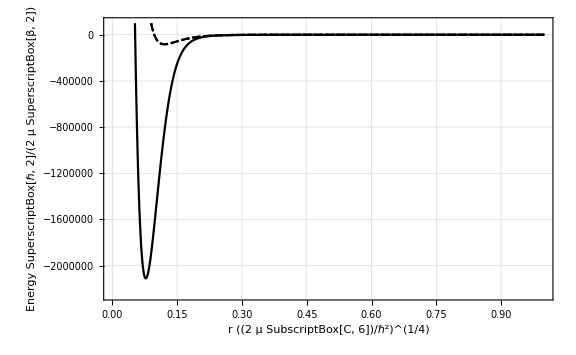

```mathematica
Plot[{SingletVDW[r],TripletVDW[r],TripletVDWNew[r]},{r,0.05,1},PlotRange->{-2.25*10^6,10^5},ImageSize->Large,GridLines->Automatic,Frame->True,FrameLabel->{"r ((2  μ SubscriptBox[C, 6])/ℏ^2)^(1/4)","Energy SuperscriptBox[ℏ, 2]/(2 μ SuperscriptBox[β, 2])"},LabelStyle->Medium(*PlotLegends->{"X^1Σ_g^+","a^3Σ_u^+"}*)]
```

```mathematica
Clear[rx, rf, r0,rmin,rmax,ltest,Etest,ksqr,BC1,BC2,nr,rGrid]
```

```mathematica
rx = 10.0*Bohrinvdw;
rf = 300*Bohrinvdw;
r0 = 40*Bohrinvdw;
rmin = 2.0*Bohrinvdw;
rmax = r0;
ltest = 0;
Etest = 10^-16;
```

```mathematica
Clear[ksqr,BC1,BC2]
```

```mathematica
vlrvdwNew[r_]:= -1/r^6;
```

```mathematica
ksqr[Ε_,l_,r_]:=(Ε -vlrvdw[r]-(l(l+1))/r^2);
BC1[Ε_,l_,r_,rx_]:=1/Sqrt[(Ε - vlrvdw[r]-(l(l+1))/r^2)^(1/2)]/.r->rx;
BC2[Ε_,l_,r_,rx_]:=D[1/Sqrt[(Ε -vlrvdw[r]-(l(l+1))/r^2)^(1/2)],r]/.r->rx;
```

```mathematica
α0sol=Flatten[Table[NDSolve[{α''[r]+ksqr[Etest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[Etest,ltest,r,rx],α'[rx]==BC2[Etest,ltest,r,rx]},α,{r,rx,rf}],{ltest,0,2}]];
α0fun=Table[α/.α0sol[[i]],{i,1,Length[α0sol]}];
nr=300;rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(α0fun[[ltest+1]][rp])^-2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,2}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,2}];
phivals=Transpose[Table[Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,α0fun[[ltest+1]],phaseintfun[[ltest+1]],rf];{rf,ArcTan[-(χm g0p-χmp g0)/(χm f0p-χmp f0)]},{ltest,0,2}],{rf,rGrid}]];
ϕfinal=Table[phivals[[i,nr,2]],{i,1,Length[phivals]}];
```

```mathematica
ϕfinal[[1]]
```

0.837793

```mathematica
CalcQuantumDefect[Ε_,l_,rmin_,rmax_,r0_,rx_,rf_,r_,nr_,U_,ϕ_]:= Module[{phaseint,αp,rp,αfun,α,f0,f0p,g0,g0p,u,up,Y,Ksr,mu},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,r0}];
αp=αfun';
g0=-α[r0]Cos[ϕ+phaseint];
g0p=αp[r0]/αfun[r0] g0+1/αfun[r0]^2 f0;
f0=α[r0]Sin[ϕ+phaseint];
f0p=αp[r0]/αfun[r0] f0-1/αfun[r0]^2 g0;
u=NDSolveValue[{-u''[r]+ (U[r]+(l(l+1))/r^2)u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
up=u';
Y = up[r]/u[r]/.r->r0;
Ksr = (Y f0 -f0p)/(Y g0 -g0p);
mu = 1/π ArcTan[Ksr];
Return[mu]
]
```

```mathematica
muSinglet = CalcQuantumDefect[0,0,rmin,rmax,r0,rx,rf,r,nr,SingletVDW,ϕfinal[[1]]]
```

-0.0312276

```mathematica
muTriplet= CalcQuantumDefect[0,0,rmin,rmax,r0,rx,rf,r,nr,TripletVDWNew,ϕfinal[[1]]]
```

0.34602

```mathematica
CalcQuantumDefect[0,0,rmin,rmax,r0,rx,rf,r,nr,TripletVDW,ϕfinal[[1]]]
```

0.346349

```mathematica
TripletQDTable = Table[{ϵ,CalcQuantumDefect[ϵ,0,rmin,rmax,r0,rx,rf,r,nr,TripletVDW,ϕfinal[[1]]]},{ϵ,-500,500,50}];
SingletQDTable=Table[{ϵ,CalcQuantumDefect[ϵ,0,rmin,rmax,r0,rx,rf,r,nr,SingletVDW,ϕfinal[[1]]]},{ϵ,-500,500,50}];
```

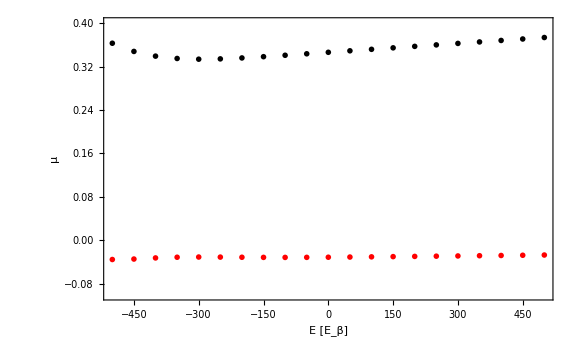

```mathematica
ListPlot[{TripletQDTable,SingletQDTable},Frame->True,FrameLabel->{"E [E_β]","μ"},PlotStyle->{Black,Red},ImageSize->Large,PlotRange->{-0.10,0.40}]
```

```mathematica
TripletQDTable2 = Table[{ϵ,CalcQuantumDefect[ϵ,0,rmin,0.45,0.45,rx,rf,r,nr,TripletVDW,ϕfinal[[1]]]},{ϵ,-500,500,50}];
TripletQDTable3 = Table[{ϵ,CalcQuantumDefect[ϵ,0,rmin,0.75,0.75,rx,rf,r,nr,TripletVDW,ϕfinal[[1]]]},{ϵ,-500,500,50}];
TripletQDTable4 = Table[{ϵ,CalcQuantumDefect[ϵ,0,rmin,0.90,0.90,rx,rf,r,nr,TripletVDW,ϕfinal[[1]]]},{ϵ,-500,500,50}];
```

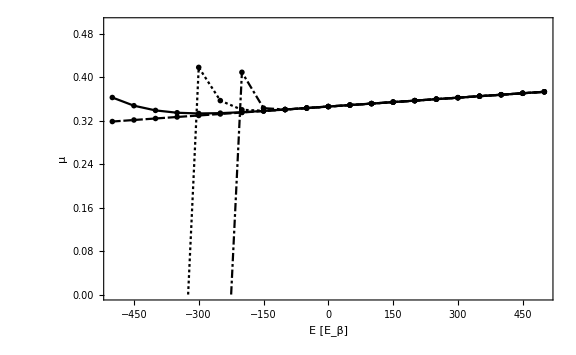

```mathematica
p1 =ListPlot[{TripletQDTable,TripletQDTable2,TripletQDTable3,TripletQDTable4},Frame->True,FrameLabel->{"E [E_β]","μ"},ImageSize->Large,Joined->True,PlotRange->{0,0.50}]
```

```mathematica
SingletQDTable2 = Table[{ϵ,CalcQuantumDefect[ϵ,0,rmin,0.45,0.45,rx,rf,r,nr,SingletVDW,ϕfinal[[1]]]},{ϵ,-500,500,50}];
SingletQDTable3 = Table[{ϵ,CalcQuantumDefect[ϵ,0,rmin,0.75,0.75,rx,rf,r,nr,SingletVDW,ϕfinal[[1]]]},{ϵ,-500,500,50}];
SingletQDTable4 = Table[{ϵ,CalcQuantumDefect[ϵ,0,rmin,0.90,0.90,rx,rf,r,nr,SingletVDW,ϕfinal[[1]]]},{ϵ,-500,500,50}];
```

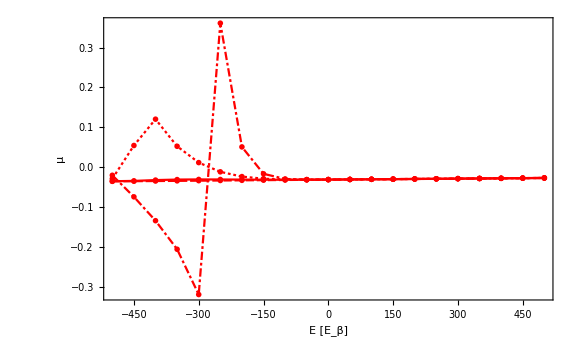

```mathematica
p2 =ListPlot[{SingletQDTable,SingletQDTable2,SingletQDTable3,SingletQDTable4},Frame->True,FrameLabel->{"E [E_β]","μ"},ImageSize->Large,Joined->True,PlotStyle->Red,PlotRange->Full]
```

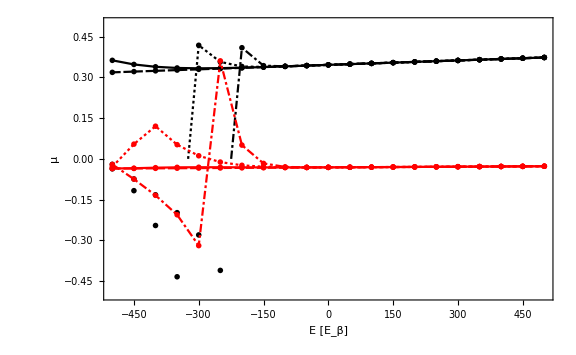

```mathematica
Show[p1,p2,PlotRange->{-0.5,0.5}]
```

```mathematica
Li7s = 1/2;
Li7i = 3/2;
Li7gs = 2.0;
mF2basis = {{1,1,1,1},{1,1,2,1},{1,0,2,2},{2,0,2,2},{2,1,2,1}};
Li7gi = 2.170903;
Li7Avdw = Li7Ainvcm*invcminHartree*Hartreeinvdw;
μbvdw=μbH*Hartreeinvdw;
μnvdw=μnH*Hartreeinvdw;
```

```mathematica
HZVDW[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μbvdw B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μnvdw B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
HZsymVDW[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(HZVDW[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7Avdw,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,4]]]+HZVDW[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7Avdw,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,2]]]+(-1)^p(-1)^l HZVDW[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7Avdw,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,4]]]+(-1)^p(-1)^l HZVDW[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7Avdw,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
HZsymLi7vdw[B_]=FullSimplify[HZsymVDW[0,0,B]];
```

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-3/2},{1,-1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{3/2,-1/2},{1,-1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
Htotalvdw[r_,B_]= HZsymLi7vdw[B]+TProjSymLi7*TripletVDWNew[r]+SProjSymLi7*SingletVDW[r];
```

```mathematica
Clear[EigensystemHZ,Eth,KsrFTEI,CC]
```

```mathematica
EigensystemHZ[B_]:=Sort[Transpose[Eigensystem[HZsymLi7vdw[B]]]]
CC[B_]:=Transpose[{EigensystemHZ[B][[1]][[2]],EigensystemHZ[B][[2]][[2]],EigensystemHZ[B][[3]][[2]],EigensystemHZ[B][[4]][[2]],EigensystemHZ[B][[5]][[2]]}];
Eth[B_]:=Table[EigensystemHZ[B][[j]][[1]],{j,1,5}]
KsrFTEI[B_]:= Transpose[CC[B]].TProjSymLi7.CC[B]*(Tan[π muTriplet])+Transpose[CC[B]].SProjSymLi7.CC[B]*(Tan[π muSinglet]);
MatrixForm[KsrFTEI[0]]
```

(1.52806 | 0.433407 | -0.306465 | 0.375341 | -0.433407
0.433407 | 1.40294 | 0.353875 | -0.433407 | 0.500455
-0.306465 | 0.353875 | 1.65317 | 0.306465 | -0.353875
0.375341 | -0.433407 | 0.306465 | 1.52806 | 0.433407
-0.433407 | 0.500455 | -0.353875 | 0.433407 | 1.40294)

```mathematica
KsrFTEIPP[B_]:= KsrFTEI[B][[1,1]];
KsrFTEIQP[B_]:=KsrFTEI[B][[2;;5,1]];
KsrFTEIPQ[B_]:=KsrFTEI[B][[1,2;;5]];
KsrFTEIQQ[B_]:=KsrFTEI[B][[2;;5,2;;5]];
```

```mathematica
Lmax=4;
```

```mathematica
αsol=Flatten[Table[NDSolve[{α''[r]+ksqr[0,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[0,ltest,r,rx],α'[rx]==BC2[0,ltest,r,rx]},α,{r,rx,rf}],{ltest,0,Lmax}]];
αfun=Table[α/.αsol[[i]],{i,1,Length[αsol]}];
rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(αfun[[ltest+1]][rp])^-2/.αsol,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,Lmax}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,Lmax}];
```

```mathematica
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=D[α[rp],rp]/.rp->r;
g0=-α[r]Cos[ϕ+phaseint[r]];
f0=α[r]Sin[ϕ+phaseint[r]];
f0p=αp/α[r] f0-1/α[r]^2 g0;
g0p=αp/α[r] g0+1/α[r]^2 f0;
χm=χminus[r,l];
χmp=χmprime[r,l];
{f0,g0,f0p,g0p,χm,χmp}]
```

```mathematica
tanphi=Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,αfun[[ltest+1]],phaseintfun[[ltest+1]],rf];-(χm g0p-χmp g0)/(χm f0p-χmp f0),{ltest,0,Lmax}]
```

{1.11069,-38.0537,-1.03903,-0.082307,0.719635}

```mathematica
phi = Table[ArcTan[tanphi[[ii]]],{ii,1,Length[tanphi]}]
```

{0.837793,-1.54452,-0.804537,-0.0821219,0.623782}

Energy Grid For Positive Energies (used for open channel long-range parameters)

```mathematica
En=500;
Emin = 10^-16;
Emax =100;
EGrid=Table[Emin+((i-1)/(En-1))^3(Emax-Emin),{i,1,En}];
```

```mathematica
calcTanGamma[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{αfun,phaseint,g0,g0p,f0,f0p,αp,α,κ,rp,gbound,gboundp,tanγ},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
κ=√-Ε;
gbound=√(κ/π rp) BesselK[l+1/2,κ rp]/.rp->rf;
gboundp=D[√(κ/π rp) BesselK[l+1/2,κ rp],rp]/.rp->rf;
tanγ =-(gbound g0p-gboundp g0)/(gbound f0p - gboundp f0);
Return[tanγ]
]
```

```mathematica
gammaTable=Table[{-EGrid[[ii]],ArcTan[calcTanGamma[0,rx,rf,r,-EGrid[[ii]],phi[[1]]]]},{ii,1,Length[EGrid]}];
```

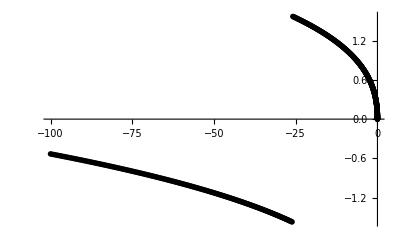

```mathematica
ListPlot[gammaTable,PlotRange->Full]
```

```mathematica
GammaTablenew=gammaTable;
For[i=1,i<Length[gammaTable],i++,
If[(gammaTable[[i+1,2]]-gammaTable[[i,2]]<-1.2),Print[i];
GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]+π,GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]]
]
```

319

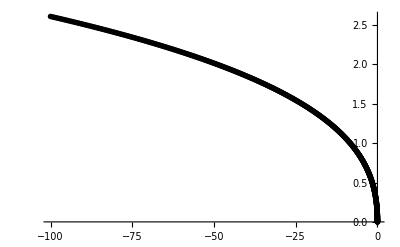

```mathematica
ListPlot[GammaTablenew]
```

```mathematica
Gammafun = Interpolation[GammaTablenew(*,InterpolationOrder->1*)];
```

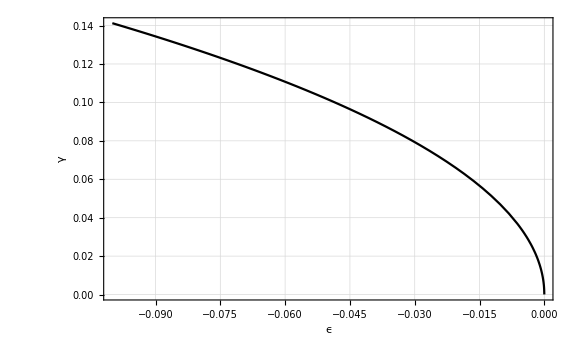

```mathematica
Plot[{Gammafun[ϵ],γ[ϵ],GammafunNew[ϵ],GammaZero[ϵ]},{ϵ,-0.1,0},Frame->True,GridLines->Automatic,FrameLabel->{"ϵ","γ"},LabelStyle->Large,ImageSize->Large,PlotStyle->{Black,Red,Blue,Green}]
```

```mathematica
CotGamma2[B_,Ε_]:= Cot[Gammafun[((Eth[B][[1]]+Ε)-Eth[B][[2]])]];
CotGamma3[B_,Ε_]:= Cot[Gammafun[((Eth[B][[1]]+Ε)-Eth[B][[3]])]];
CotGamma4[B_,Ε_]:= Cot[Gammafun[((Eth[B][[1]]+Ε)-Eth[B][[4]])]];
CotGamma5[B_,Ε_]:= Cot[Gammafun[((Eth[B][[1]]+Ε)-Eth[B][[5]])]];
CotGammaMatrix[B_,Ε_]:=DiagonalMatrix[{CotGamma2[B,Ε],CotGamma3[B,Ε],CotGamma4[B,Ε],CotGamma5[B,Ε]}];
```

```mathematica
CotGamma2New[B_,Ε_]:= Cot[GammaC6[((Eth[B][[1]]+Ε)-Eth[B][[2]])]];
CotGamma3New[B_,Ε_]:= Cot[GammaC6[((Eth[B][[1]]+Ε)-Eth[B][[3]])]];
CotGamma4New[B_,Ε_]:= Cot[GammaC6[((Eth[B][[1]]+Ε)-Eth[B][[4]])]];
CotGamma5New[B_,Ε_]:= Cot[GammaC6[((Eth[B][[1]]+Ε)-Eth[B][[5]])]];
CotGammaMatrixNew[B_,Ε_]:=DiagonalMatrix[{CotGamma2New[B,Ε],CotGamma3New[B,Ε],CotGamma4New[B,Ε],CotGamma5New[B,Ε]}];
```

```mathematica
bmax = 1200;
bmin = 0;
bn = 100;
bgrid = Table[(bmax-bmin)/bn i,{i,0,bn}];
Etest = 10^-16;
```

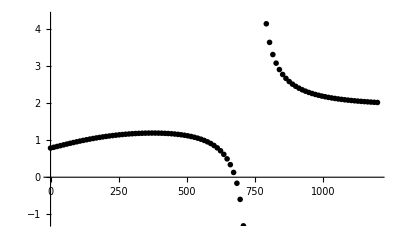

```mathematica
KtildeFTEI[B_,Ε_]:= KsrFTEIPP[B]-KsrFTEIPQ[B].Inverse[KsrFTEIQQ[B]+CotGammaMatrix[B,Ε]].KsrFTEIQP[B];
KtildeFTEINew[B_,Ε_]:= KsrFTEIPP[B]-KsrFTEIPQ[B].Inverse[KsrFTEIQQ[B]+CotGammaMatrixNew[B,Ε]].KsrFTEIQP[B];
ListPlot[{Table[{bgrid[[ii]],KtildeFTEI[bgrid[[ii]],Etest]},{ii,1,bn+1}],Table[{bgrid[[ii]],KtildeFTEINew[bgrid[[ii]],Etest]},{ii,1,bn+1}]}]
```

```mathematica
CalcTanEta[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,gs,fs,fsp,gsp,k,tanη,αfun,phaseint,α,αp},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs =g[l,k,r];
gsp=dgdr[l,k,r];
tanη=(fs f0p-f0 fsp)/(gs f0p-f0 gsp)/.r->rf;
Return[tanη]
]
```

```mathematica
EtaTable=Table[{EGrid[[ii]],ArcTan[CalcTanEta[ltest,rx,rf,r,EGrid[[ii]],phi[[1]]]]},{ii,1,Length[EGrid]}];
```

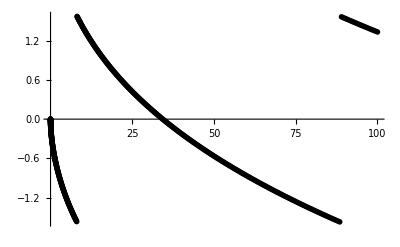

```mathematica
ListPlot[EtaTable]
```

```mathematica
EtaTablenew=EtaTable;
For[i=1,i<Length[EtaTable],i++,
If[(EtaTable[[i+1,2]]-EtaTable[[i,2]]>1.2),Print[i];
EtaTablenew[[i+1;;Length[EtaTable],2]]=EtaTablenew[[i+1;;Length[EtaTable],2]]-π,EtaTablenew[[i+1;;Length[EtaTable],2]]=EtaTablenew[[i+1;;Length[EtaTable],2]]]
]
```

216

480

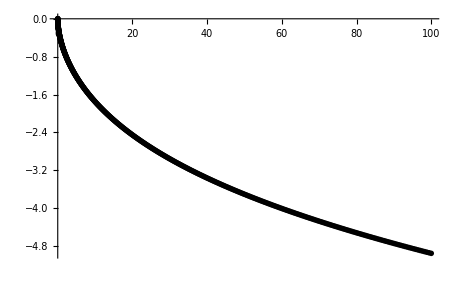

```mathematica
ListPlot[EtaTablenew]
```

```mathematica
Etafun=Interpolation[EtaTablenew,InterpolationOrder->1]
```

InterpolatingFunction[…]

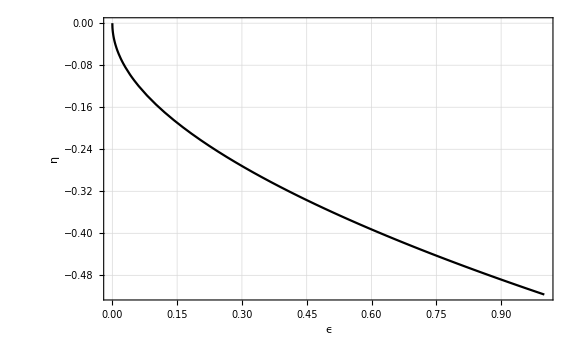

```mathematica
Plot[{Etafun[ϵ],η[ϵ]},{ϵ,0,1},Frame->True,GridLines->Automatic,FrameLabel->{"ϵ","η"},LabelStyle->Large,ImageSize->Large,PlotStyle->{Black,Red}]
```

```mathematica
CalcA[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,fs,fsp,gs,gsp,k,A,αfun,phaseint,α,αp,tanη,Wfsf0,Wgsf0,Wfsg0,Wgsg0},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,rf];
fsp=dfdr[l,k,rf];
gs=g[l,k,rf];
gsp=dgdr[l,k,rf];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
A=-((Wfsg0 -tanη Wgsg0)/(Wgsf0+tanη Wfsf0));
Return[A]
]
```

```mathematica
ATable=Table[{EGrid[[ii]],CalcA[ltest,rx,rf,r,EGrid[[ii]],phi[[1]]]},{ii,1,Length[EGrid]}];
```

```mathematica
Afun = Interpolation[ATable,InterpolationOrder->1]
```

InterpolatingFunction[…]

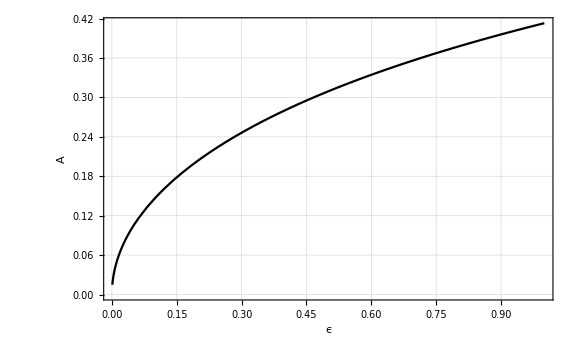

```mathematica
Plot[{Afun[ϵ]},{ϵ,0.001,1},Frame->True,GridLines->Automatic,FrameLabel->{"ϵ","A"},LabelStyle->Large,ImageSize->Large]
```

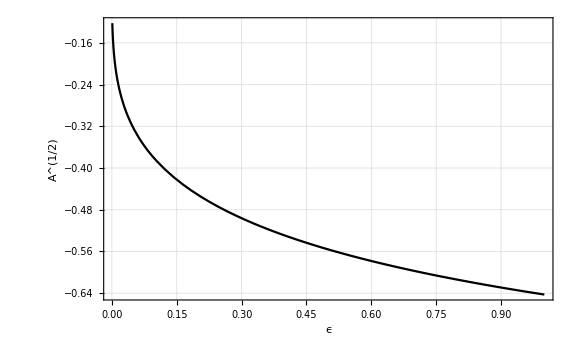

```mathematica
Plot[{-Sqrt[Afun[ϵ]],AOneHalf[ϵ]},{ϵ,0.001,1},Frame->True,GridLines->Automatic,FrameLabel->{"ϵ","A^(1/2)"},LabelStyle->Large,ImageSize->Large,PlotStyle->{Black,Red}]
```

```mathematica
CalcG[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,k,tanη,G,fs,fsp,gs,gsp,αfun,phaseint,Wfsf0,Wgsf0,Wfsg0,Wgsg0,α,αp},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[ Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs=g[l,k,r];
gsp=dgdr[l,k,r];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
G=-(Wfsg0*Wfsf0+Wgsg0*Wgsf0)/(Wfsf0^2+Wgsf0^2)/.r->rf;
(*G =-((g0 gsp-g0p gs)+tanη(g0 fsp-g0p fs))/((f0 gsp - f0p gs)+tanη (f0 fsp - f0p fs))/.r->rf;*)
Return[G]
]
```

```mathematica
GTable=Table[{EGrid[[ii]],CalcG[ltest,rx,rf,r,EGrid[[ii]],phi[[1]]]},{ii,1,Length[EGrid]}];
```

```mathematica
Gfun = Interpolation[GTable,InterpolationOrder->1]
```

InterpolatingFunction[…]

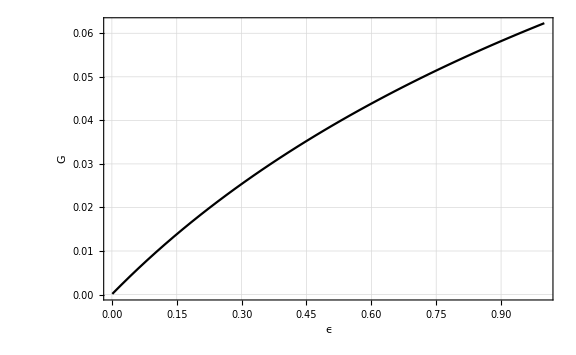

```mathematica
Plot[{Gfun[ϵ],G[ϵ]},{ϵ,0.001,1},Frame->True,GridLines->Automatic,FrameLabel->{"ϵ","G"},LabelStyle->Large,ImageSize->Large,PlotStyle->{Black,Red}]
```

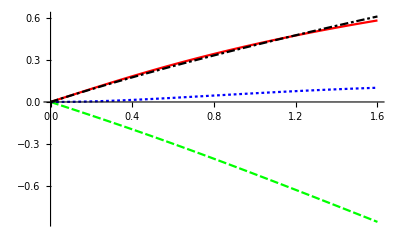

```mathematica
Plot[{Afun[κ^2],Etafun[κ^2],Gfun[κ^2],Gammafun[-κ^2],(AOneHalfzero[κ^2])^2,etazerofun[κ^2],Gzero[κ^2],GammaZero[-κ^2]},{κ,0,1.6},PlotStyle->{Red,Green,Blue,Black,Red,Green,Blue,Black}]
```

```mathematica
Etest = 10^-3;
```

```mathematica
KFTEITable = Table[{bgrid[[ii]], Sqrt[Afun[Etest]] (KtildeFTEI[bgrid[[ii]],Etest]^-1+Gfun[Etest])^-1 Sqrt[Afun[Etest]]},{ii,1,bn+1}];
KFTEITableNew = Table[{bgrid[[ii]], AOneHalfC6[Etest] (KtildeFTEINew[bgrid[[ii]],Etest]^-1+GC6[Etest])^-1 AOneHalfC6[Etest]},{ii,1,bn+1}];
```

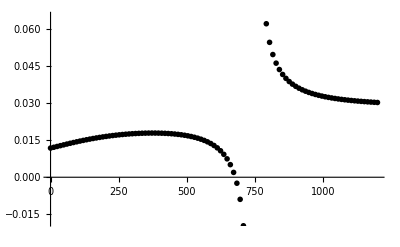

```mathematica
ListPlot[{KFTEITable,KFTEITableNew}]
```

```mathematica
KFTEnergyfun[B_,Ε_]:= Sqrt[Afun[Ε]] (KtildeFTEI[B,Ε]^-1+Gfun[Ε])^-1 Sqrt[Afun[Ε]];
SFTEnergyfun[B_,Ε_]:= Exp[ⅈ Etafun[Ε]] ((1+ⅈ KFTEnergyfun[B,Ε])/(1-ⅈ KFTEnergyfun[B,Ε])) Exp[ⅈ Etafun[Ε]];
KFTEnergyfunNew[B_,Ε_]:= AOneHalfC6[Ε] (KtildeFTEI[B,Ε]^-1+GC6[Ε])^-1 AOneHalfC6[Ε];
SFTEnergyfunNew[B_,Ε_]:= Exp[ⅈ EtaC6[Ε]] ((1+ⅈ KFTEnergyfunNew[B,Ε])/(1-ⅈ KFTEnergyfunNew[B,Ε])) Exp[ⅈ EtaC6[Ε]];
```

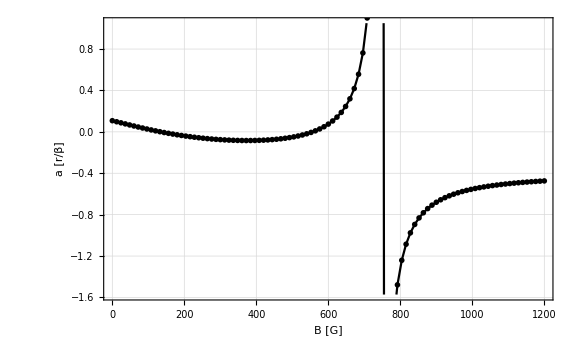

```mathematica
SFTEITable= Table[Exp[ⅈ Etafun[Etest]] ((1+ⅈ KFTEITable[[ii,2]])/(1-ⅈ KFTEITable[[ii,2]])) Exp[ⅈ Etafun[Etest]],{ii,1,bn+1}];
ascatFTEITable=Table[{bgrid[[ii]],Re[-1/(ⅈ Sqrt[Etest]) ((SFTEITable[[ii]]-1)/(SFTEITable[[ii]]+1))]},{ii,1,bn+1}];
SFTEITableNew= Table[Exp[ⅈ EtaC6[Etest]] ((1+ⅈ KFTEITableNew[[ii,2]])/(1-ⅈ KFTEITableNew[[ii,2]])) Exp[ⅈ EtaC6[Etest]],{ii,1,bn+1}];
ascatFTEITableNew=Table[{bgrid[[ii]],Re[-1/(ⅈ Sqrt[Etest]) ((SFTEITableNew[[ii]]-1)/(SFTEITableNew[[ii]]+1))]},{ii,1,bn+1}];
ListPlot[{ascatFTEITable,ascatFTEITableNew},Frame->True,FrameLabel->{"B [G]", "a [r/β]"},GridLines->Automatic,LabelStyle->Large,ImageSize->Large,Joined->True,PlotStyle->{Black,Blue}]
```

```mathematica
cotdeltafun[Ε_,B_]:=(1-Tan[Etafun[Ε]]KFTEnergyfun[B,Ε])/(Tan[Etafun[Ε]]+KFTEnergyfun[B,Ε]);
cotdeltafunNew[Ε_,B_]:=(1-Tan[EtaC6[Ε]]KFTEnergyfunNew[B,Ε])/(Tan[EtaC6[Ε]]+KFTEnergyfunNew[B,Ε]);
```

```mathematica
ascatfun[B_,Ε_]:= -1/(Sqrt[Ε] cotdeltafun[Ε,B]); 
ascatfunNew[B_,Ε_]:= -1/(Sqrt[Ε] cotdeltafunNew[Ε,B]);
```

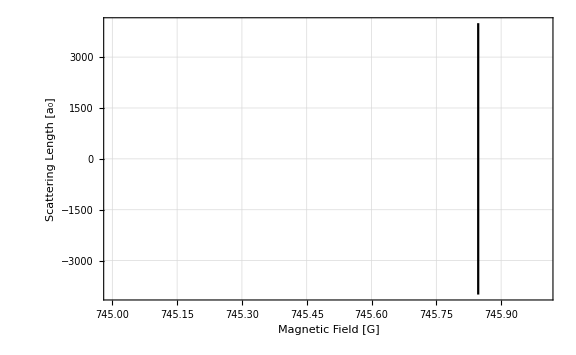

```mathematica
Plot[{ascatfun[B,Etest]/Bohrinvdw,ascatfunNew[B,Etest]/Bohrinvdw},{B,745,746},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->Large,FrameLabel->{"Magnetic Field [G]","Scattering Length [a_0]" },PlotStyle->{Black,Red},PlotRange->{{745,746},{-4000,4000}}]
```

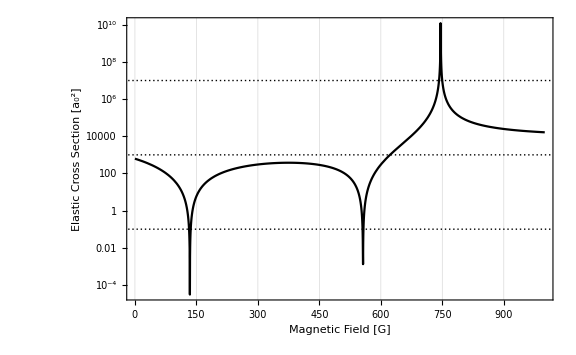

```mathematica
pmqdt =LogPlot[{4π(ascatfun[B,Etest]/Bohrinvdw)^2,4π(ascatfunNew[B,Etest]/Bohrinvdw)^2},{B,0,1000},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->Large,FrameLabel->{"Magnetic Field [G]","Elastic Cross Section [a_0^2]" },PlotStyle->{Black,Blue}]
```

```mathematica
logderdat =  Import["/Users/niravmehta/Documents/GitHub/LiScattering/Li7FR.dat"];
```

Import::nffil: File /Users/niravmehta/Documents/GitHub/LiScattering/Li7FR.dat not found during Import.

```mathematica
ListLinePlot[logderdat[[100;;155]]]
```

Part::take: Cannot take positions 100 through 155 in $Failed.

ListLinePlot::lpn: $Failed⟦100;;155⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[$Failed⟦100;;155⟧]

```mathematica
p10 =ListLogPlot[ Table[{logderdat[[ii,1]],4π (logderdat[[ii,2]])^2},{ii,1,Length[logderdat]}],Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->Large,Joined->True,FrameLabel->{"Magnetic Field [G]","Elastic Cross Section [a_0^2]" },PlotStyle->{Red}]
```

-Graphics-

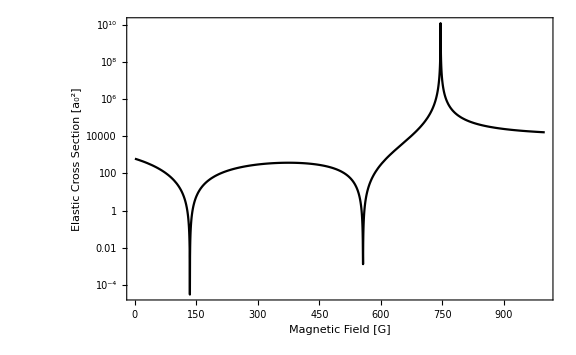

```mathematica
Show[p10,pmqdt,PlotRange->Full]
```